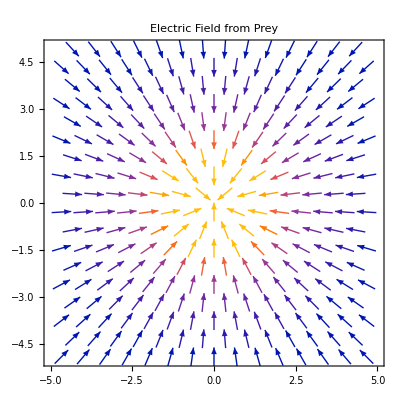

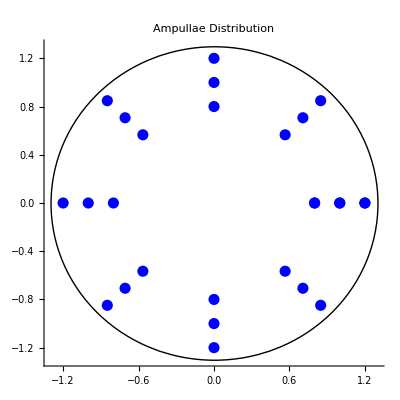

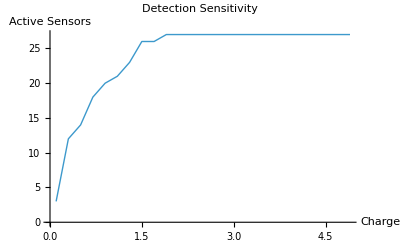

```mathematica
(* Electrosensory Modeling of Ampullae of Lorenzini*)
(*Constants and Parameters*)
k=1.0;
seawaterConductivity=5.0;
ampullaeThreshold=0.1; 
preyCharge=3;

(*Electric Field Model-Fixed formula*)
electricFieldMagnitude[x_,y_,qx_,qy_]:=k*preyCharge/((x-qx)^2+(y-qy)^2+0.01)^1.5

(*Vector Field Visualization*)
VectorPlot[{-x/((x^2+y^2+0.1)^1.5),-y/((x^2+y^2+0.1)^1.5)},{x,-5,5},{y,-5,5},VectorPoints->15,PlotLabel->"Electric Field from Prey"]

(*Ampullae Distribution*)
ampullaePos=Table[{r*Cos[theta],r*Sin[theta]},{theta,0,2*Pi,Pi/4},{r,0.8,1.2,0.2}];
ampullaeFlat=Flatten[ampullaePos,1];

(*Visualize Ampullae Distribution*)
Graphics[{PointSize[0.02],Blue,Point[ampullaeFlat],Black,Circle[{0,0},1.3]},PlotLabel->"Ampullae Distribution",Axes->True]

(*Dynamic Prey Detection-FIXED*)
Manipulate[Module[{fieldValues,activePos,maxField},(*Calculate field values at each ampulla position*)fieldValues=Map[electricFieldMagnitude[#[[1]],#[[2]],px,py]&,ampullaeFlat];
maxField=Max[fieldValues];
(*Find active ampullae logic*)activePos=Pick[ampullaeFlat,UnitStep[fieldValues-ampullaeThreshold],1];
(*Debug*)Print["Max field: ",maxField," Threshold: ",ampullaeThreshold," Active: ",Length[activePos]];
Graphics[{PointSize[0.015],Gray,Point[ampullaeFlat],PointSize[0.025],Red,Point[activePos],PointSize[0.03],Green,Point[{px,py}],Black,Circle[{0,0},1.3]},PlotRange->{{-4,4},{-4,4}},PlotLabel->"Active: "<>ToString[Length[activePos]]<>"/"<>ToString[Length[ampullaeFlat]]<>" (Max Field: "<>ToString[NumberForm[maxField,5]]<>")"]],{px,-3,3},{py,-3,3}]

(*Electric Field Contour Plot with Ampullae*)
Manipulate[Show[ContourPlot[electricFieldMagnitude[x,y,px,py],{x,-4,4},{y,-4,4},Contours->20,ColorFunction->"Rainbow"],Graphics[{Black,PointSize[0.015],Point[ampullaeFlat],Red,PointSize[0.025],Point[{px,py}]}]],{px,-3,3},{py,-3,3}]

(*Sensitivity Analysis-FIXED*)
sensitivityData=Table[{charge,Count[Map[k*charge/((#[[1]]-1)^2+(#[[2]]-1)^2+0.01)^1.5&,ampullaeFlat],x_/;x>ampullaeThreshold]},{charge,0.1,5,0.2}];

ListLinePlot[sensitivityData,AxesLabel->{"Charge","Active Sensors"},PlotLabel->"Detection Sensitivity",PlotStyle->Thick]

(*Multiple Prey Detection-FIXED*)
Manipulate[Module[{field1,field2,totalField,activePos},field1=Map[electricFieldMagnitude[#[[1]],#[[2]],p1x,p1y]&,ampullaeFlat];
field2=Map[electricFieldMagnitude[#[[1]],#[[2]],p2x,p2y]&,ampullaeFlat];
totalField=field1+field2;
activePos=Pick[ampullaeFlat,UnitStep[totalField-ampullaeThreshold],1];
Graphics[{PointSize[0.015],Gray,Point[ampullaeFlat],PointSize[0.025],Red,Point[activePos],PointSize[0.03],Green,Point[{p1x,p1y}],Blue,Point[{p2x,p2y}],Black,Circle[{0,0},1.3]},PlotRange->{{-4,4},{-4,4}},PlotLabel->"Two Prey Detection - Active: "<>ToString[Length[activePos]]]],{p1x,-3,3},{p1y,-3,3},{p2x,-3,3},{p2y,-3,3}]

(*Real-time field strength display*)
Manipulate[Module[{fieldValues,maxField,minField},fieldValues=Map[electricFieldMagnitude[#[[1]],#[[2]],px,py]&,ampullaeFlat];
maxField=Max[fieldValues];
minField=Min[fieldValues];
Column[{Graphics[{PointSize[0.015],MapThread[{If[#2>ampullaeThreshold,Red,Gray],Point[#1]}&,{ampullaeFlat,fieldValues}],PointSize[0.03],Green,Point[{px,py}],Black,Circle[{0,0},1.3]},PlotRange->{{-4,4},{-4,4}},PlotLabel->"Field Strength Visualization"],"Max Field: "<>ToString[NumberForm[maxField,3]],"Min Field: "<>ToString[NumberForm[minField,3]],"Threshold: "<>ToString[ampullaeThreshold],"Active Sensors: "<>ToString[Count[fieldValues,x_/;x>ampullaeThreshold]]}]],{px,-3,3},{py,-3,3}]
```